## Schmied - Using Mathematica for Quantum Mechanics

## Wolfram Language Overview

# 1.1 Introduction

To write comments, press Alt+7, then type comment.
To minimize, maximize sections, double click on the brackets on the right of the page.
To look for documentation, type ? followed by the function:

```mathematica
?Factorial
```

n! gives the factorial of n.

```mathematica
?Simplify
```

Simplify[expr] performs a sequence of algebraic and other transformations on expr and returns the simplest form it finds. 
Simplify[expr,assum] does simplification using assumptions.

### 1.1.1. Exercises.

Do calculations and understand their structures.
Q1.1

```mathematica
N[Zeta[3]]
```

1.20206

N[exp] evaluates expression numerically, N[exp, n] gives result to n-digit precision
Zeta[s] calculates Riemann Zeta function of number s.

Q1.2

```mathematica
%^2
```

1.44494

% refers to the last result generated, %n or Out[n] refers to the nth output line.

Q1.3

```mathematica
Integrate[Sin[x]*Exp[-x], {x, 0, Infinity}]
```

1/2

Integrate[f, {x, x_min, x_max}] gives a definite integral. Integrate[f , x] gives indefinite integral.

Ctrl+_ to write a subscript. 
Ctrl+b to write bold.
Ctrl+i to write italic.

Q1.4

```mathematica
N[Pi, 20]
```

3.1415926535897932385

Calculates numerical value of Pi up to 20 digits precision.

Q1.5

```mathematica
ClebschGordan[{100,10},{200,-12}, {110, -2}]
```

1/14 8261297798499109361013742279092521767681 √(769248995636473/29722486922289527474028523218044627174628912734745629147957669733897130076853320942746928207329)

```mathematica
N[1/14 8261297798499109361013742279092521767681 √(769248995636473/29722486922289527474028523218044627174628912734745629147957669733897130076853320942746928207329),10]
```

0.09493167387

Calculates Clebsch-Gordan coefficient {\bra 100,10; 200,-12 | 110, -2 /ket} (analytic and numeric).

Q 1.6

```mathematica
Limit[Sin[x]/x, x -> 0]
```

1

Calculates Limit[ f[x], x -> x*]

Q1.7

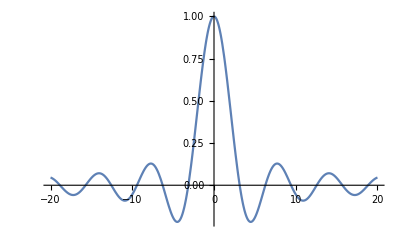

```mathematica
Plot[Sin[x]/x, {x, -20, 20}, PlotRange->All]
```

Q1.8

```mathematica
F[c_,imax_] := Abs[NestWhile[#^2+c&, 0., Abs[#]≤2&, 1, imax]] ≤2
With[{n = 100, imax= 1000},
Graphics[Raster[Table[Boole[!F[x+I*y,imax]], {y, -2,2,1/n}, {x, -2,2,1/n}]]]]
```

-Graphics-

Q1.9

```mathematica
MandelbrotSetPlot[]
```

-Graphics-

# 1.2 Variables and Assignments